# Answers to Exercises Najeeb Hassan 9988342

## Week 1

### Q1 :

```mathematica
Table[Replace[Replace[Replace[x, RotI], RefB], RotIinv], {x, 1, 26, 1} ]
```

```mathematica
{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}
```

### Q2 :

```mathematica
RotI={1->5,2->11,3->13,4->6,5->12,6->7,7->4,8->17,9->22,10->26,11->14,12->20,13->15,14->23,15->25,16->8,17->24,18->21,19->19,20->16,21->1,22->9,23->2,24->18,25->3,26->10}
```

```mathematica
RotIinv={5->1,11->2,13->3, 6 -> 4, 12 -> 5, 7-> 6, 4->7,17->8,22->9,26->10,14->11,20->12,15->13,23->14,25->15,8->16,24->17,21->18,19->19,16->20,1->21,9->22,2->23,18->24,3->25,10->26}
```

```mathematica
Table[Replace[Replace[Replace[x, RotI], RefB], RotIinv], {x, 1, 26, 1} ]
```

```mathematica
{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}
```

```mathematica
Q3:
EnigmaGuts={1->8,8->1,2->11, 3 -> 13, 4 -> 19, 5 -> 6, 6 -> 5, 7 -> 16, 8 -> 1, 9 -> 14, 10 -> 12, 11 -> 2, 12 -> 10, 13 -> 3, 14 -> 9, 15 -> 21, 16 -> 7, 17 -> 26, 18 -> 25, 19 -> 4, 20 -> 22, 21 -> 15, 22 -> 20, 23 -> 24, 24 -> 23, 25 -> 18 , 26 -> 17}

Q4:
Table[ReplaceAll [x, EnigmaGuts] , {x, 1, 26, 1}]
{8,11,13,19,6,5,16,1,14,12,2,10,3,9,21,7,26,25,4,22,15,20,24,23,18,17}
```

```mathematica
Q5:
Table [Enigma1 [1, n] , {n, 0, 25, 1} ]
```

```mathematica
{8,10,11,16,2,26,10,20,6,3,18,25,17,22,7,18,10,8,12,3,21,25,2,26,20,18}
```

```mathematica
Q6:
list1=Table [Enigma1 [1, n] , {n, 0, 25, 1} ]
```

```mathematica
list2= Range[0,25]
```

```mathematica
Enigma1[10,1]
```

```mathematica
MapThread[Enigma1,{list1,{list2}]
```

```mathematica
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
```

## Week 2

### Q1:

```mathematica
EnigmaMachine[text_,key_]:= MapThread[Enigma1,{text, Table[key+n,{n, 0, Length[text]-1, 1}]}]
```

### Q2:

```mathematica
EnigmaMachine[{1,2,3,4,5},28]
```

```mathematica
{11,3,12,9,22}
```

```mathematica
EnigmaMachine[EnigmaMachine[{1,2,3,4,5}, 28],28]
```

```mathematica
{1,2,3,4,5}
```

### Q3:

```mathematica
plain={1,3,4,23,9,2,12,8}
```

```mathematica
cypher={17,4,14,6,17,3,4,23,8,8,19,3,1,24,22,11,6,22,15}
```

```mathematica
CyFrag = {3,4,23,8,8,19,3,1}
```

```mathematica
CribCycle = [3,4,23,8,1]
```

```mathematica
crib = {1 -> 3, 2 -> 4, 3 -> 23, 4-> 8, 8-> 1}
```

```mathematica
CribLocation = 6
```

the number of elements in the crib cycle is 5

### Q4:

```mathematica
Cyfrag = {3,4,23,8,8,19,3,1}
Distance between each member of the crib cycle:
(1 -> 3) = 1
```

```mathematica
(2 -> 4) = 2
```

```mathematica
(3 -> 23) = 3
```

```mathematica
(4 ->8) = 4
```

```mathematica
(8->1) = 8
```

### Q5:

```mathematica
Bombe[plain_,cyfrag_,k_]:=If[Enigma1[plain[[1]],k]==cyfrag[[1]]&&cyfrag[[1]]==plain[[2]]&&
Enigma1[plain[[2]],k+1] == cyfrag[[2]] && cyfrag[[2]]  == plain[[3]] &&
Enigma1[plain[[3]], k+2] == cyfrag[[3]] && cyfrag[[3]] == plain [[4]] &&
         Enigma1[plain[[4]], k+3] == cyfrag[[4]] && cyfrag[[4]] == plain[[8]] &&
         Enigma1[plain[[8]], k+7] == cyfrag[[8]] && cyfrag[[8]] == plain[[1]],{"YES!!!",k},{"no"}]

Table[Bombe[plain,cyfrag,k],{k,0,25,1}]

{{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"},{"YES!!!",19},{"no"},{"no"},{"no"},{"no"},{"no"},{"no"}}
```

The key setting found for the cribbed plaintext by using the Bombe expression is 19.

### Q6: the Key setting for the whole ciphertext is 14.

### Q7: 3423881921

## Week 3

```mathematica
Q1:
m=12345; a= 11111; GCD[m,a]
EulerPhi[m]
Mod[a^EulerPhi[m],m]
```

1

6576

1

```mathematica
m=123; a= 11; GCD[m,a]
EulerPhi[m]
Mod[a^EulerPhi[m],m]
```

1

80

1

#### Q2:

```mathematica
ExtendedGCD[7, 17]
Mod[5 * 13, 17]
{1, {5, -2}}
14

[107]:= GCD[148 953 050, 179 424 673]
PowerMod[123 456 789, EulerPhi[179 424 673] - 1, 179 424 673]

1
172 609 538

Mod[135 798 642 * 172 609 538, 179 424 673]

21 562 478

Mod[123 456 789 * 21 562 478, 179 424 673]

135 798 642

PowerMod[123 456 789, -1, 179 424 673]

172 609 538

Clear[x];
Solve[ 12 x == 8, {x}, Modulus -> 16]

{{x -> 2 + 4 C[1]}}

Clear[x];
Solve[ 12 x == 8, {x}, Modulus -> 16] /. Table[{C[1] -> n}, {n, 0, 4, 1}]

{{{x -> 2}}, {{x -> 6}}, {{x -> 10}}, {{x -> 14}}, {{x -> 18}}}

x /. Solve[ 12 x == 8, {x}, Modulus -> 16]

{2 + 4 C[1]}

x /. Solve[ 13 x == 1, {x}, Modulus -> 16]

{5}
```

#### Q3:

```mathematica
ChineseRemainder[{1,0,0},{11,13,17}]
ChineseRemainder[{0,1,0},{11,13,17}]
ChineseRemainder[{0,0,1},{11,13,17}]
```

```mathematica
221
1496
715
```

```mathematica
u1 = ChineseRemainder[{1,0,0},{13,29,64}]
u2 = ChineseRemainder[{0,1,0},{13,29,64}]
u3 = ChineseRemainder[{0,0,1},{13,29,64}]
```

7424

13312

3393

```mathematica
ChineseRemainder[{10,5,7}, {13,29,64}]
```

19783

```mathematica
Mod[10 * u1 + 5 * u2 + 7 * u3, 13 * 29 * 64]
```

19783

### Q4.

```mathematica
<<"FiniteFields`"
```

```mathematica
k = 111111
```

111111

```mathematica
Prime[k]
```

1456667

```mathematica
p = 1456667
```

1456667

```mathematica
PrimeQ[p]
PowerList[GF[p,1]][[2]]
```

True

{2}

```mathematica
Primitive1 = PowerList[GF[p,1]][[2]]
```

{2}

```mathematica
KeyB = 1500
```

1500

```mathematica
KeyA = 2500
```

2500

```mathematica
publiccA = PowerMod [Primitive1, KeyA, p]
```

{824424}

```mathematica
publiccB = PowerMod[Primitive1, KeyB,p]
```

{767659}

```mathematica
PowerMod[767659,KeyA,p]
```

1058208

```mathematica
PowerMod[824424,KeyB,p]
```

1058208

#### Q5

```mathematica
k = 111111
```

111111

```mathematica
Prime[k]
```

1456667

```mathematica
p = 145667;
```

```mathematica
a = Primitive1;
```

```mathematica
r = RandomInteger[{0,p-2}]
```

85393

```mathematica
u = 123;
```

```mathematica
R = PowerMod[a,r,p]
```

{6919}

```mathematica
cB = PowerMod[a, mB,p]
```

{70988}

```mathematica
S=Mod[PowerMod[cB,r,p] u,p]
```

{3313}

```mathematica
mB=1640;
```

```mathematica
Mod[S*PowerMod[PowerMod[R,mB,p],-1,p],p]
```

{123}

#### Q6

```mathematica
p = 145667;
```

```mathematica
a = Primitive1;
```

```mathematica
mA = 2500;
```

```mathematica
r = RandomInteger[{0,p-2}]
```

```mathematica
106752
```

```mathematica
u = 123;
```

```mathematica
S =.;
```

```mathematica
R = PowerMod[a,r,p]
```

```mathematica
106752
```

```mathematica
u = 123;
```

```mathematica
S =.;
```

```mathematica
R = PowerMod[a,r,p]
```

```mathematica
{27140}
```

```mathematica
S/.Solve[{r S==u-mA *R},{S},Modulus->p-1][[1]]
```

```mathematica
36463
```

```mathematica
cA = PowerMod [Primitive1, KeyA, p]
```

```mathematica
{44974}
```

```mathematica
R = PowerMod[a,r,p]
```

```mathematica
{54012}
```

```mathematica
cA=2500; R = PowerMod[a,r,p] ; S = 36363;
```

```mathematica
PowerMod[a,u,p]==Mod[ PowerMod[cA,R,p]*PowerMod[R,S,p],p]
```

```mathematica
{True}
```

#### Q7

```mathematica
pB=Prime[1450]
qB=Prime[1500]
nB=pB*qB
phiB=EulerPhi[nB]
```

12109

12553

152004277

151979616

```mathematica
eB=RandomInteger[{1,nB}];
While[GCD[eB,phiB]≠1,eB=RandomInteger[{1,nB}]];
eB
ExtendedGCD[eB,phiB]
```

82430045

{1,{-34328395,18618886}}

```mathematica
dB=-34328395;
Mod[eB*dB,phiB]
```

1

```mathematica
nB=99052741;eB=81119923;dB=-34328395;
m=12345678;
c=PowerMod[m,eB,nB]
```

38447790

```mathematica
PowerMod[c,dB,nB]
```

47918729

```mathematica
NumberTheory'NumberTheoryFunctions'
```

NumberTheory' NumberTheoryFunctions'

```mathematica
a=ChineseRemainder[{1,0},{9733,10177}]
b=ChineseRemainder[{0,1},{9733,10177}]
```

45287650

53765092

```mathematica
p=9733;q=10177;d=16391903;c=38447790;c1=Mod[c,p]
c2=Mod[c,q]
d1=Mod[d,p-1]
d2=Mod[d,q-1]
m1=PowerMod[c1,d1,p]
m2=PowerMod[c2,d2,q]
```

2440

9261

3215

8543

4237

9706

```mathematica
n=99052741;Mod[m1*a+m2*b,n]
```

52757097

#### Q8

```mathematica
m=11111111;c=PowerMod[m,dB,nB]
```

```mathematica
90296910
```

## Week 4

#### Q1

```mathematica
Manipulate[ContourPlot[y^2==x^3-5 x+3,{x,-3,3},{y,-4,4},Axes->True],{a, -5,-3}]
```

```mathematica
Manipulate[ContourPlot[y^2==x^3-5 x+3,{x,-3,3},{y,-4,4},Axes->True ,Epilog->Line[{{-3,4},{4,-3}}]], {a, -5,-3}]
```

#### Q2 The intersection line only crosses over one point once it is on -3.

### Q3

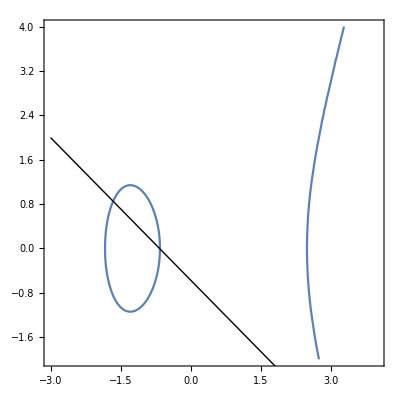

```mathematica
ContourPlot[x^3 - 5x - 3==y^2,{x,-3,4},{y,-2,4}, PlotRange-> {-4,4}, Axes->True, Epilog-> Line[ {{-3,2},{4,-4}}]]
```

#### Q4

```mathematica
NSolve[ {y^2==x^3-5 x+3,y==-x+1},{x,y}]
```

{{x→-1.61803,y→2.61803},{x→2.,y→-1.},{x→0.618034,y→0.381966}}

#### Q5

```mathematica
p =11;
```

```mathematica
Table[ Solve[ {y^2== x^3-5 x + 3, x==u},{x,y}, Modulus->p], {u, 0, p-1}]
```

{{{x→0,y→5},{x→0,y→6}},{},{{x→2,y→1},{x→2,y→10}},{{x→3,y→2},{x→3,y→9}},{{x→4,y→5},{x→4,y→6}},{{x→5,y→2},{x→5,y→9}},{},{{x→7,y→5},{x→7,y→6}},{},{{x→9,y→4},{x→9,y→7}},{}}

#### Q6

```mathematica
p=11;
Clear[x];
ec=x^3-5x+3;
il=4x+1;
Factor[il^2-ec,Modulus->p]
```

10 (2+x) (7+x) (8+x)

```mathematica
x=Mod[{-2,-7,-8},p]
y=Mod[4*x+1,p]
```

{9,4,3}

{4,6,2}

```mathematica
InterpolatingPolynomial[{{5,3},{2,7}},5]
```

3

```mathematica
EllipticAdd[p_,a_,b_,c_,P_List,Q_List]:=Module[{lam,x3,y3,P3},Which[P=={O},R=Q,Q=={O},R=P,P[[1]]≠Q[[1]],lam=Mod[(Q[[2]]-P[[2]]) PowerMod[Q[[1]]-P[[1]],-1,p],p];
x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
y3=Mod[-(lam (x3-P[[1]])+P[[2]]),p];
R={x3,y3},(P==Q)&&(P≠{O}),lam=Mod[(3*P[[1]]^2+2 a*P[[1]]+b) PowerMod[2 P[[2]],-1,p],p];
x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
y3=Mod[-(lam (x3-P[[1]])+P[[2]]),p];
R={x3,y3},(P[[1]]==Q[[1]])&&(P[[2]]≠Q[[2]]),R={O}];R]
```

```mathematica
p=11;a=0;b=6;c=3;EllipticAdd[p,a,b,c,{5,3},{2,7}]
EllipticAdd[p,a,b,c,{5,3},{5,3}]
EllipticAdd[p,a,b,c,{2,6},{2,7}]
EllipticAdd[p,a,b,c,{5,7},{O}]
EllipticAdd[p,a,b,c,{5,7},{5,5}]
EllipticAdd[p,a,b,c,{O},{2,7}]
```

{7,7}

{10,1}

{O}

{5,7}

{O}

{2,7}

#### Q7

```mathematica
FactorInteger[432]
IntegerDigits[432,2]
IntegerDigits[432/2,2]
IntegerDigits[432/3,2]
```

{{2,4},{3,3}}

{1,1,0,1,1,0,0,0,0}

{1,1,0,1,1,0,0,0}

{1,0,0,1,0,0,0,0}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[7],P[6]],	 	EllipticAdd[p,a,b,c,P[4],P[3]]]
EllipticAdd[p,a,b,c,P[7],P[4]]
```

{O}

{19,0}

{341,175}

#### Q8

```mathematica
QAlice=EllipticAdd[p,a,b,c,P[7],P[1]]
QBob=EllipticAdd[p,a,b,c,P[8],P[5]]
```

{162,663}

{341,688}

#### Q9

```mathematica
<<FiniteFields`
```

```mathematica
z16=GF[2,4]
```

GF[2,{1,0,0,1,1}]

```mathematica
FullForm[%]
```

GF[2,List[1,0,0,1,1]]

```mathematica
FieldIrreducible[z16,x]
```

FieldIrreducible[GF[2,{1,0,0,1,1}],{9,4,3}]

```mathematica
Characteristic[z16]
```

2

```mathematica
ExtensionDegree[z16]
```

4

```mathematica
FieldSize[z16]
```

16

```mathematica
dd=z16[{0,0,1,1}]
```

{0,0,1,1}_2

```mathematica
dd+dd
```

0

```mathematica
dd-dd
```

0

```mathematica
ee=z16[{1,1,0,0}]
```

{1,1,0,0}_2

```mathematica
dd ee
```

{1,0,1,1}_2

```mathematica
dd/ee
```

{0,0,1,0}_2

```mathematica
ee=z15[{1,1,0,0}]
```

z15[{1,1,0,0}]

```mathematica
dd
```

{0,0,1,1}_2

```mathematica
dd ee
```

z15[{1,1,0,0}] {0,0,1,1}_2

```mathematica
dd/ee
```

({0,0,1,1}_2)/z15[{1,1,0,0}]

#### Q10

```mathematica
ee=z16[{1,1,0,0}]
```

{1,1,0,0}_2

```mathematica
(dd^n)^3+ee (dd^n)^2
```

{0,0,1,1}_2^(3 n)+{0,0,1,1}_2^(2 n) {1,1,0,0}_2

```mathematica
y^2+x y
```

{52,60,10}

```mathematica
x^3+ee x^2
```

{{0,1,0,0}_2,64,{0,1,0,0}_2}

```mathematica
Z2mEllipticAdd[a_,c_,P_List,Q_List]:=Module[{lam,x3,y3,P3,R},Which[P=={O},R=Q,Q=={O},R=P,ToElementCode[P[[1]]]≠ToElementCode[Q[[1]]],lam=(Q[[2]]+P[[2]])/(Q[[1]]+P[[1]]);x3=lam^2+lam+a+P[[1]]+Q[[1]];y3=lam (x3+P[[1]])+x3+P[[2]];R={x3,y3},((ToElementCode[P[[1]]]==ToElementCode[Q[[1]]])&&(ToElementCode[P[[2]]]==ToElementCode[Q[[2]]]))&&(P≠{O}),lam=P[[1]]+P[[2]]/P[[1]];x3=lam^2+lam+a;y3=P[[1]]^2+(lam+1) x3;R={x3,y3},(ToElementCode[P[[1]]]==ToElementCode[Q[[1]]])&&(ToElementCode[P[[2]]]≠ToElementCode[Q[[2]]]),R={O}];R]
```

```mathematica
P=.;a=ee;c=0;P[0]={x,y};P[i_]:=P[i]=Z2mEllipticAdd[a,c,P[i-1],P[i-1]]
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[7],P[6]],	 	EllipticAdd[p,a,b,c,P[4],P[3]]]
EllipticAdd[p,a,b,c,P[7],P[4]]
```

```mathematica
{Mod[Subscript[{1,1,0,0}, 2],863],Mod[-688-66 (-341+Mod[Subscript[{1,1,0,0}, 2],863]),863]}
```

## Week 5

```mathematica
RandomInteger[1,40]
{0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0,0,1,0,1,1,0,0,0,1,0,0,1,0,0}

AliceBasis = Table[RandomInteger[1,40]]
{0,1,0,1,1,1,1,0,1,1,0,1,0,1,0,1,1,1,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,1,0,1,0,0,1,0}

AliceData = Table[RandomInteger[1,40]]
{1,1,0,0,1,0,1,1,1,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,1}

BobBasis = Table[RandomInteger[1,40]]
{1,0,1,0,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0,1,0,1,0,1,1,0,1,0,1,1}

if[
AliceData == Bobdata
EqualBases = 1
else
EqualBases = 0
]

if[0]

if[
AliceBasis = BobBasis
Bobdata = AliceData
EqualBases
]

if[{1,1,0,0,1,0,1,1,1,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,1}]


Bobdata = Intersection[AliceBasis,BobBasis]
{0,1}
```